```mathematica
kHz = 10^3;
```

```mathematica
ramseyDisplacementUncert[Ω_, f_, tf_, T_]:= 2*Ω*tf*Sinc[(2*π*f*tf)/2]*Sin[(2*π*f*(T+tf))/2];
Normal[Series[ramseyDisplacementUncert[Ω, f,tf, T], {f,0,2}]];
```

```mathematica
γ[γ0_, f_, tc_]:= γ0*Sinc[2*π*f*tc];
p[g_, f_, t_,t0_,α_]:= Cos[2*Abs[γ[g, f, t]]*Abs[α]*Sin[Arg[γ[g, f, t, t0]] + Arg[α]]]^4
Δp[g_, f_, t_, t0_,α_]:= Sqrt[p[γ[g, f, t],α](1-p[γ[g, f, t],α])]
Δω[g_,t_, f_,α_] := FullSimplify[Δp[γ[g,f,t],α]/Abs[D[p[g,f, t,α],δ]]]
```

```mathematica
(*timing parameters*)
tCatUse = 200*10^-6;
tTickleUse = 200*10^-6;

(*resource parameters to use*)
αUse=0.9;
γ0Use = Sqrt[1.25];

(*detuning parameters*)
detuningPts = 100; 
fMax = 20*kHz;
df = fMax/detuningPts;
```

### Compare Fisher Information for two ion (Ca-HCl) and three ion (Ca - HCl - Ca)

```mathematica
eps=10^-16;
pb[γ0_,f_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, f, tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^2;
pd[γ0_,f_,tTick_,tCat_,α_]:= Sin[2*γ[γ0, f, tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^2;
pbb[γ0_,f_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, f, tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4;
pdd[γ0_,f_,tTick_,tCat_,α_]:= Sin[2*γ[γ0,f,tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4;
pud[γ0_,f_,tTick_,tCat_,α_]:= 1-Sin[2*γ[γ0,f,tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4-Cos[2*γ[γ0,f,tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4;
FITwo[γ0_,f_,tTick_,tCat_,α_]:= (D[pb[γ0,f,tTick,tCat, α], f])^2/Max[pb[γ0,f,tTick,tCat, α], eps]+(D[pd[γ0,f,tTick,tCat, α], f])^2/Max[pd[γ0,f,tTick,tCat, α], eps];
FIThree[γ0_,f_,tTick_,tCat_,α_]:= (D[pbb[γ0,f,tTick,tCat, α], f])^2/Max[pbb[γ0,f,tTick,tCat, α], eps]+(D[pdd[γ0,f,tTick,tCat, α], f])^2/Max[pdd[γ0,f,tTick,tCat, α], eps]+(D[pud[γ0,f,tTick,tCat, α], f])^2/Max[pud[γ0,f,tTick,tCat, α], eps];


FullSimplify[FIThree[γ0,f,tTick,tCat,α]/FITwo[γ0,f,tTick,tCat,α]]
```

$Aborted

### Fisher Information and CR bound for Classical Ramsey Interferometry

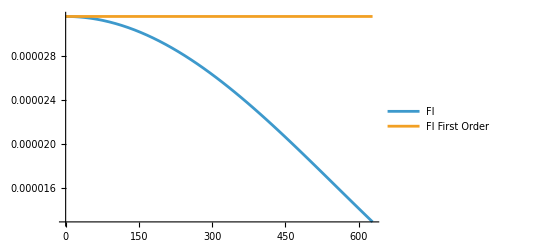

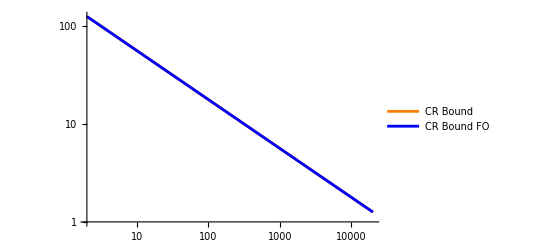

```mathematica
ramseyDisplacement[γ0_, f_, tTick_, tAcc_]:= 2*γ0*Sinc[2*π*f*tTick/2]*Sin[(2*π*f*(tAcc+tTick))/2](*Exp[ⅈ*δ*(T+tf)]*);
ramseyDisplacementFO[γ0_, f_, tTick_, tAcc_]:=Normal[Series[ramseyDisplacement[γ0, f, tTick, tAcc], {f,0,1}]]
FRamsey[f_,tTick_,tAcc_,γ0_]:= 4*(Abs[D[ramseyDisplacement[γ0, f, tTick, tAcc], f]])^2;
FRamseyFO[f_,tTick_,tAcc_,γ0_]:= 4*(Abs[D[ramseyDisplacementFO[γ0, f, tTick, tAcc], f]])^2;
FFRamseyFO =FRamseyFO[f,tTick,tAcc,γ0]/.{tTick->tCatUse,γ0->γ0Use,tAcc->tTickleUse};
FFRamsey =FRamsey[f,tTick,tAcc,γ0]/.{tTick->tCatUse,γ0->γ0Use,tAcc->tTickleUse};
fRamseyopt = Table[f, {f,1,1000}][[PositionLargest[Table[FFRamsey, {f,1,10000}]]]][[1]];
Plot[{FFRamsey, FFRamseyFO}, {f,0,2*π*100}, PlotLegends->{"FI", "FI First Order"}]
LogLogPlot[{1/Sqrt[NN*FFRamsey/.{f->fRamseyopt}],
1/Sqrt[NN*FFRamseyFO/.{f->fRamseyopt}]},{NN, 2,2*10^4}, 
PlotLegends->{"CR Bound", "CR Bound FO"}, PlotStyle->{Orange, Blue, Black}]
```

## Normal Cat Interferometer SQL

540

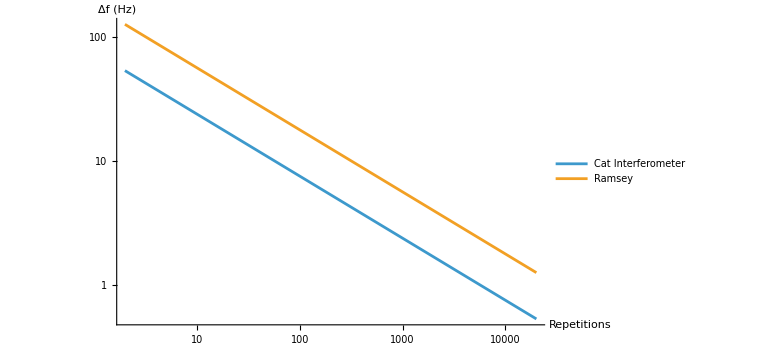

```mathematica
eps = 10^-15;
pbb[γ0_,f_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, f, tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4;
pdd[γ0_,f_,tTick_,tCat_,α_]:= Sin[2*γ[γ0,f,tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4;
pud[γ0_,f_,tTick_,tCat_,α_]:= 1-Sin[2*γ[γ0,f,tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4-Cos[2*γ[γ0,f,tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^4;
F[g_,f_,tTick_,tCat_,α_]:= (D[pbb[γ0,f,tTick,tCat, α], f])^2/Max[pbb[γ0,f,tTick,tCat, α], eps]+(D[pdd[γ0,f,tTick,tCat, α], f])^2/Max[pdd[γ0,f,tTick,tCat, α], eps]+(D[pud[γ0,f,tTick,tCat, α], f])^2/Max[pud[γ0,f,tTick,tCat, α], eps];


(*Fisher Info*)
FF =F[γ0,f,tTick,tCat,α]/.{tTick->tTickleUse, γ0->γ0Use,α->αUse,tCat->tCatUse};
FFRamsey =FRamsey[f, tTick,tAcc,γ0]/.{tTick->tCatUse, γ0->γ0Use,tAcc->tTickleUse};

(*Find Optimal Detuning for Cat Interferometer*)
fCatopt = Table[f, {f,1,fMax}][[PositionLargest[Table[FF, {f,1,fMax}]]]][[1]]

(*Fisher Info Calculations*)
CRBoundunEnt = 1/Sqrt[numExperiments*F[g,f,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, f->fCatopt, α->αUse, tCat->tCatUse}];
sqlBound = 1/Sqrt[numExperiments*FRamsey[f,tTickle,tAcc, γ0]/.{tAcc->tTickleUse,γ0->γ0Use,tTickle->tCatUse, f->fRamseyopt}];
CRBoundunEntPlot = LogLogPlot[{CRBoundunEnt,
sqlBound},{numExperiments, 2,2*10^4}, 
PlotLegends->{"Cat Interferometer", "Ramsey"}, AxesLabel->{Style["Repetitions", 16], 
Style["Δf (Hz)", 16]}, GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 16], AxesStyle->Directive[Thickness[0.0025]]]
(*Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\CRBoundunEnt.svg", CRBoundunEnt]
```

```mathematica
(*Fisher information gain from cat unterferometer versus ramsey*)
fisherInfoCat = N[F[γ0,f,tTick,tCat,α]/.{tTick->tTickleUse, γ0->γ0Use, f->fCatopt, α->αUse, tCat->tCatUse}];
fisherInfoCat/10^-5
fisherInfoRamsey = Limit[FFRamsey, f->0]

fisherInfoRatioCatRamsey = fisherInfoCat/fisherInfoRamsey;
N[10Log10[fisherInfoRatioCatRamsey]]
```

17.5816

0.0000315827

7.45609

## Entangled Cat SQL

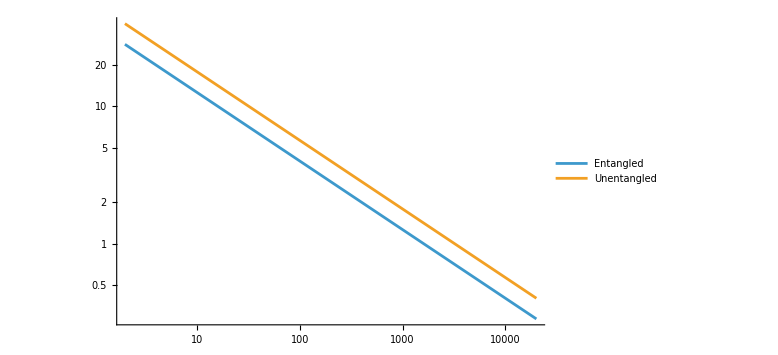
-Graphics-RepsΔf (Hz)

```mathematica
eps = 10^-15;
(*Entangled Cat Interferometer Populations*)
pbbEnt[γ0_,f_,tTick_,tCat_,α_]:= 1/2 Cos[4*γ[γ0, f, tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^2;
pddEnt[γ0_,f_,tTick_,tCat_,α_]:= 1/2 Cos[4*γ[γ0, f, tTick]*α*Sin[π/2+2*π*f*(tTick+tCat)]]^2;
pdbEnt[γ0_,f_,tTick_,tCat_,α_]:= Sin[4*γ[γ0, f, tCat]*α*Sin[π/2+2*π*f*(tCat+tTick)]]^2;

(*Entangled Fisher Info*)
FEnt[γ0_,f_,tTick_,tCat_,α_]:= (D[pbbEnt[γ0,f,tTick,tCat, α], f])^2/Max[pbbEnt[γ0,f,tTick,tCat, α], eps]+(D[pddEnt[γ0,f,tTick,tCat, α], f])^2/Max[pbbEnt[γ0,f,tTick,tCat, α], eps]+(D[pdbEnt[γ0,f,tTick,tCat, α], f])^2/Max[pdbEnt[γ0,f,tTick,tCat, α], eps];
FFEnt =FEnt[γ0,f,tTick,tCat,α]/.{tTick->tTickleUse, γ0->γ0Use, α->αUse, tCat->tCatUse};


fEntopt = Table[f, {f,1,fMax}][[PositionLargest[Table[FFEnt, {f,1,fMax}]]]][[1]];

(*Bounds*)
CRBoundEnt = 1/Sqrt[numExperiments*FEnt[γ0,f,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, f->fEntopt, α->αUse, tCat->tCatUse}];
sqlBound = 1/Sqrt[numExperiments*F[γ0,f,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, f->fCatopt, α->αUse, tCat->tCatUse}];

(*Plot*)
CRBoundEntPlot= Labeled[LogLogPlot[{CRBoundEnt,sqlBound},{numExperiments, 2,2*10^4}, 
PlotLegends->Placed[LineLegend[{Style["Entangled", 20], Style["Unentangled", 20]}, LegendMarkerSize->25], {0.75, 0.75}], GridLines->Automatic,
ImageSize->Large, TicksStyle->Directive["Label", 18]], {Style["Reps", 20], 
Style["Δf (Hz)", 20]}, {Bottom, Left}]
(*Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Posters and Presentations\\Josh\\ATC\\images\\simulation_images\\CRBoundEnt.svg", CRBoundEntPlot]*)
```

```mathematica
(*Fisher information gain from entangled cat interferometer versus unentangled cat interferometer*)
fisherInfoCatEnt= N[FEnt[γ0,f,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, f->fEntopt, α->αUse, tCat->tCatUse}]
fisherInfoCatunEnt = N[F[γ0,f,tTick,tCat, α]/.{tTick->tTickleUse, γ0->γ0Use, f->fCatopt, α->αUse, tCat->tCatUse}]

fisherInfoRatioCatEnt= N[fisherInfoCatEnt/fisherInfoCatunEnt];
N[20*Log10[Sqrt[fisherInfoRatioCatEnt]]]
```

0.000625124

0.000312562

3.0103

### Maximum Likelihood Estimator

```mathematica
pb[γ0_,δ_,tTick_,tCat_,α_]:= Cos[2*γ[γ0, δ, tTick]*α*Sin[π/2+δ*(tTick+tCat)]]^2;
pbϕ[ϕ_, d_]:= 1/2+(1-d)/2 Cos[2*ϕ];
pdϕ[ϕ_,d_]:= 1/2-(1-d)/2 Cos[2*ϕ];
pbbϕ[ϕ_, d_]:= Cos[ϕ]^4;
pddϕ[ϕ_, d_]:= Sin[ϕ]^4;
pbbϕ[ϕ_, d_]:= (1/2+(1-d)/2 Cos[2*ϕ])^2
pddϕ[ϕ_, d_]:= (1/2-(1-d)/2 Cos[2*ϕ])^2
pdbϕ[ϕ_, d_]:= 1-pddϕ[ϕ, d]-pbbϕ[ϕ, d];
pbbEntϕ[ϕ_, d_]:= 1/2*(1/2+(1-d)/2 Cos[4*ϕ]);
pddEntϕ[ϕ_, d_]:= 1/2*(1/2+(1-d)/2 Cos[4*ϕ]);
pdbEntϕ[ϕ_, d_]:= (1/2-(1-d)/2 Cos[4*ϕ]);

pbδ[δ_,d_]:= 1/2+(1-d)/2 Cos[2*2*α*Sinc[(δ-δ0)*t] * Sin[δ*(t+t0)+θ]];
pdδ[δ_,d_]:= 1/2-(1-d)/2 Cos[2*2*α*Sinc[(δ-δ0)*t] * Sin[δ*(t+t0)+θ]];
pbbδ[δ_,d_]:= (1/2+(1-d)/2 Cos[2*2*α*Sinc[(δ-δ0)*t] * Sin[δ*(t+t0)+θ]])^2;
pddδ[δ_,d_]:= (1/2-(1-d)/2 Cos[2*2*α*Sinc[(δ-δ0)*t] * Sin[δ*(t+t0)+θ]])^2;
pdbδ[δ_,d_]:= 1-pddδ[δ,d]-pbbδ[δ,d];
pbbEntδ[δ_,d_]:= 1/2*(1/2+(1-d)/2 Cos[4*2*α*Sinc[(δ-δ0)*t] * Sin[δ*(t+t0)+θ]]);
pddEntδ[δ_,d_]:= 1/2*(1/2+(1-d)/2 Cos[4*2*α*Sinc[(δ-δ0)*t] * Sin[δ*(t+t0)+θ]]);
pdbEntδ[δ_,d_]:= (1/2-(1-d)/2 Cos[4*2*α*Sinc[(δ-δ0)*t] * Sin[δ*(t+t0)+θ]]);
```

```mathematica
LSingle[Nb_, Nd_, pb_, pd_, ϕ_, d_]:= Factorial[(Nb+Nd)]/(Factorial[(Nb)]*Factorial[(Nd)])*pb[ϕ, d]^Nb*pd[ϕ, d]^Nd;
DLogLSingle = FullSimplify[D[Log[LSingle[Nb, Nd, pbϕ, pdϕ, ϕ, d]], ϕ]];
FullSimplify[Solve[DLogLSingle ==0, ϕ, Assumptions->{Nd>=0 && Nb>=0 && d>=0 && d<=1}]]
```

{{ϕ→ConditionalExpression[π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[π (1/2+C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 ArcTan[(-Nb+Nd)/((-1+d) (Nb+Nd)),-(√(((-2+d) Nb+d Nd) (-2 Nd+d (Nb+Nd))))/(√((-1+d)^2 (Nb+Nd)^2))]+π C[1], C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 ArcTan[(-Nb+Nd)/((-1+d) (Nb+Nd)),(√(((-2+d) Nb+d Nd) (-2 Nd+d (Nb+Nd))))/(√((-1+d)^2 (Nb+Nd)^2))]+π C[1], C[1]∈ℤ]}}

```mathematica
LDouble[Nbb_, Ndb_, Ndd_, pbb_, pdb_, pdd_, ϕ_, d_]:= Factorial[(Ndd+Ndb+Nbb)]/(Factorial[(Ndd)]*Factorial[(Ndb)]*Factorial[(Nbb)])*pbb[ϕ,d]^Nbb*pdb[ϕ,d]^Ndb*pdd[ϕ,d]^Ndd;
DLogLDouble = FullSimplify[D[Log[LDouble[Nbb, Ndb, Ndd, pbbϕ, pdbϕ, pddϕ, ϕ, d]], ϕ]];
SolDouble = FullSimplify[Solve[DLogLDouble==0 && 0<=ϕ<=π/2, ϕ, Assumptions->{Ndb>=0 && Ndd>=0 && Nbb>=0 && d>=0 && d<=1 && 2*Nbb + Ndb >= 0}]]
```

{{ϕ→0},{ϕ→π/2},{ϕ→ConditionalExpression[1/2 ArcSec[((-1+d) (Nbb+Ndb+Ndd))/(-Nbb+Ndd)], ]}}

```mathematica
LEntDouble[Nbb_, Ndb_, Ndd_, pbbEnt_, pdbEnt_, pddEnt_, ϕ_, d_]:= Factorial[(Ndd+Ndb+Nbb)]/(Factorial[(Nbb)]*Factorial[(Ndb)]*Factorial[(Ndd)])*pbbEnt[ϕ,d]^Nbb*pdbEnt[ϕ,d]^Ndb*pddEnt[ϕ,d]^Ndd;
DLogEntLDouble = FullSimplify[D[Log[LEntDouble[Nbb, Ndb, Ndd, pbbEntϕ, pdbEntϕ, pddEntϕ, ϕ, d]], ϕ]];
SolEntDouble = FullSimplify[Solve[DLogEntLDouble==0 && 0 <= ϕ <=π/2, ϕ, Assumptions->{Ndb>=0 && Ndd>=0 && Nbb>=0 && d>=0 && d<=1 && 2*Nbb + Ndb >= 0}]]
```

{{ϕ→0},{ϕ→π/4},{ϕ→π/2},{ϕ→ConditionalExpression[1/4 (π+ArcSec[((-1+d) (Nbb+Ndb+Ndd))/(Nbb-Ndb+Ndd)]), ]},{ϕ→ConditionalExpression[1/4 ArcSec[-((-1+d) (Nbb+Ndb+Ndd))/(Nbb-Ndb+Ndd)], ]}}

```mathematica
LogL = Nbb1 * Log[pbbδ[δ1, d]] + Ndd1 * Log[pddδ[δ1, d]]+ Ndb1 * Log[pdbδ[δ1, d]] + Nbb2 * Log[pbbδ[δ2, d]] + Ndd2 * Log[pddδ[δ2, d]]+ Ndb2 * Log[pdbδ[δ2, d]]
```

Ndd1 Log[(1/2-1/2 (1-d) Cos[4 α Sin[(t+t0) δ1+θ] Sinc[t (-δ0+δ1)]])^2]+Nbb1 Log[(1/2+1/2 (1-d) Cos[4 α Sin[(t+t0) δ1+θ] Sinc[t (-δ0+δ1)]])^2]+Ndb1 Log[1-(1/2-1/2 (1-d) Cos[4 α Sin[(t+t0) δ1+θ] Sinc[t (-δ0+δ1)]])^2-(1/2+1/2 (1-d) Cos[4 α Sin[(t+t0) δ1+θ] Sinc[t (-δ0+δ1)]])^2]+Ndd2 Log[(1/2-1/2 (1-d) Cos[4 α Sin[(t+t0) δ2+θ] Sinc[t (-δ0+δ2)]])^2]+Nbb2 Log[(1/2+1/2 (1-d) Cos[4 α Sin[(t+t0) δ2+θ] Sinc[t (-δ0+δ2)]])^2]+Ndb2 Log[1-(1/2-1/2 (1-d) Cos[4 α Sin[(t+t0) δ2+θ] Sinc[t (-δ0+δ2)]])^2-(1/2+1/2 (1-d) Cos[4 α Sin[(t+t0) δ2+θ] Sinc[t (-δ0+δ2)]])^2]